## Bayesian Statistics, Assignment for Tuesday, Nov. 26

## Reading

Note that I am deliberately giving Chapter 12 short shrift. We did a hairy derivation that culminated in Eq. 12.10 on p. 180. My handout on that was called “A Multi-Dimensional Continuum of Hypotheses.” Those that have time and want some serious challenge should push through to the end of the handout and derive the formulas given in Michael I. Jordan’s Stat 260 class. I have not yet found the time.

In the Thursday, Nov. 22 class, we built our intuition about Monte Carlo methods by generating a representative sample of quarterly iPhone sales. Of course you don’t need Monte Carlo methods to generate a representative sample for such a simple distribution, but the idea was to see in detail how Monte Carlo methods work.

Now we are ready to apply Monte Carlo methods to the posterior, which is the product of a prior and a likelihood. We want a representative sample from the posterior. Everything I can think of that you need to understand for Chapter 13 is in place. So study the heck out of Chapter 13 (pp. 193-211), and perhaps before Tuesday some of you could come tell me what more we should elaborate on. I hope you entirely understand it, but it will make for a more interesting class if you have something you want to probe.

## For Problem Set 15 — Exercises to go Along with Chapter 13

## 1. A Slightly Different Procedure

Recall steps 5-8 of the procedure we used to generate the representative iPhone sales:

5. Draw a random number uniformly distributed between 0 and 1.
6. If the random number is less than the appropriate ratio, your position is the new quarter.
7. If the random number is greater than the appropriate ratio, your position is unchanged.
8. Either way, the computer reports a position (that is either the new or unchanged position).

My formula for the “appropriate ratio” was:

rBrian=(P(possible new position))/(P(current position)+P(possible new position))

I hope I convinced everyone that not only does it work, but then I spoke about “ergodicity” and why this specific choice of ratios works.

But now, let’s look at Donovan and Mickey’s appropriate ratio! It is:

rDonovanAndMickey=the minimum of((P(possible new position))/(P(current position)),1)

Let’s apply my formula and their formula to a terribly simple parent distribution:

```mathematica
unitSalesByFiscalHalfInMillions = {
{"H1", 75},
{"H2", 175}
};
annualUnitSales = Total[unitSalesByFiscalHalfInMillions][[2]];
normalizedUnitSales = N[unitSalesByFiscalHalfInMillions[[All,2]]/= annualUnitSales]
```

{0.3,0.7}

Above is the normalized distribution.

Now we need to compute the ratios. Here are the “appropriate ratios” done the way I showed you:

```mathematica
rBrian[n_,m_]:=Round[normalizedUnitSales[[m]]/(normalizedUnitSales[[m]]+normalizedUnitSales[[n]]),0.01];
rDonovanAndMickey[n_,m_]:=Round[Min[normalizedUnitSales[[m]]/normalizedUnitSales[[n]],1],0.01];
brianRatios={
{"1->2", rBrian[1,2]},
{"2->1", rBrian[2,1]}
};
donovanAndMickeyRatios={
{"1->2", "______"},
{"2->1", "______"}
};
TableForm[brianRatios]
```

1->2 | 0.7
2->1 | 0.3

You know my “appropriate ratios” work.

Fill in Donovan and Mickey’s “appropriate ratios” using their procedure. Round to two decimal places.

```mathematica
TableForm[donovanAndMickeyRatios]
```

1->2 | ______
2->1 | ______

## 2. Applying the Slightly Different Procedure

(a) Write down the day of the month of your birthday:

(b) Below is a place you can make your Fiscal Half 1 (H1) and Fiscal Half 2 (H2) tallies. If your answer to (a) was odd, put the first tally in the H1 column. If your answer to (a) is even, but the first tally in the H2 column.

PLACE FOR TALLIES/NOTES
















(c) Since there are only two columns, you don’t need to do a coin flip to decide whether you go left or right! Either direction leads to the other column. You just need a random number between 0 and 1.

On the facing page is a table of 31 random numbers. Starting on the row that is your birthday, run the procedure 19 times and make 19 more tallies. Don’t use my appropriate ratios. Use the Donovan and Mickey ratios you filled in in Problem 1.

```mathematica
smallIterations=31;
randomReals=Round[RandomReal[{0,1},smallIterations],0.01];
rounds=Range[1,smallIterations];

TableForm[Transpose[{rounds,randomReals}]]
```

1 | 0.7
2 | 0.08
3 | 0.25
4 | 0.19
5 | 0.51
6 | 0.25
7 | 0.93
8 | 0.62
9 | 0.6
10 | 0.86
11 | 0.78
12 | 0.48
13 | 0.34
14 | 0.11
15 | 0.84
16 | 0.77
17 | 0.87
18 | 0.01
19 | 0.85
20 | 0.7
21 | 0.34
22 | 0.79
23 | 0.18
24 | 0.34
25 | 0.61
26 | 0.86
27 | 0.99
28 | 0.61
29 | 0.97
30 | 0.12
31 | 0.66

## 3. Comparing with Expectations

You ended up with 20 tallies total. From the parent distribution, if there are 20 tallies, you expect 20*0.3=6 in H1 and 20*0.7=14 in H2.

What is the square root of 6? This is the expected standard deviation for H1. Is your H1 within or near 1 standard deviation of 6? E.g., near the range 3 to 9? It is a random process, so it doesn’t have to be, but it usually is.

## 4. Summary

In one sentence, what is the qualitative and quantitative difference between Donovan and Mickey’s “appropriate ratios” and the ones I showed you?


In class, we will add everyone’s tallies together and see how representative our combined sample is.

In the meantime, I let Mathematica off the leash for half a second or so, so it could run the procedure 100,000 times.

```mathematica
position=RandomInteger[{1,2}];
accumulator = ConstantArray[0,2];
iterations = 100000;
randomNumbers=RandomReal[1,iterations];
accumulate[z_]:=(
newPosition=3 - position;
ratio=Min[normalizedUnitSales[[newPosition]]/normalizedUnitSales[[position]],1];
position = If[RandomReal[]<ratio,newPosition,position];
accumulator[[position]]+=1;
)
Map[accumulate,randomNumbers];
expected=normalizedUnitSales*iterations;
```

Below is a bar chart showing what Mathematica got with Donovan and Mickey’s procedure. The representative sample matches the parent distribution so well I cannot tell the difference.

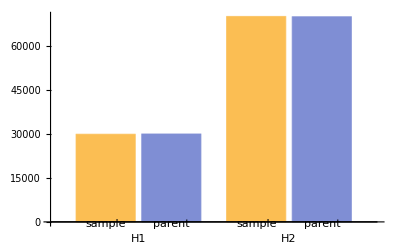

```mathematica
BarChart[Transpose[{accumulator,expected}],ChartLabels->{unitSalesByFiscalHalfInMillions[[All,1]],{"sample","parent"}}]
```

The ENIAC (Electronic Numerical Integrator and Computer) on which the first electronic Monte Carlo calculations were done.

The ENIAC was built to do artillery range calculations. The plugs change the conditions (latitude, longitude, altitude, direction, muzzle velocity, and wind all affect targeting). Artillery operators would consult tables printed by this machine and carried into the field or aboard naval vessels.

I don’t know more details, but I expect it is yet another effort that only gets more fascinating the more you look at it.